# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Separating by parity\UPO for alfa 0.84 and k 20

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
randomregion=RandomPoint[Disk[{1,0.5},0.2],1000];
(*randomregion=RandomPoint[Disk[{-1.01,0.58},0.01],10];*)
(*randomregion=Table[{i,0},{i,0,1.9990,0.001}];*)
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=-randomregion;
randomregion//Length
```

1000

```mathematica
{x0,x1,y0,y1}={0.9,1.2,0.35,0.6};
region=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/50},{j,y0,y1,(y1-y0)/50}],1];
region//Length
```

2601

```mathematica
{x0,x1,y0,y1}={1.04783500,1.04785,0.46795,0.467990};
randomregion=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/40},{j,y0,y1,(y1-y0)/40}],1];
```

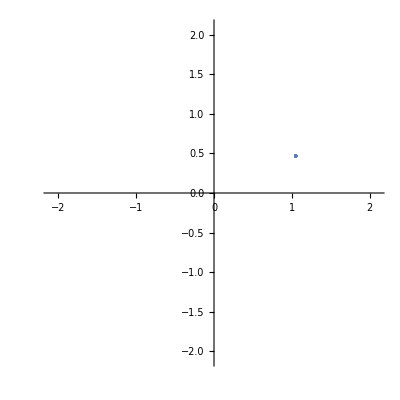

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

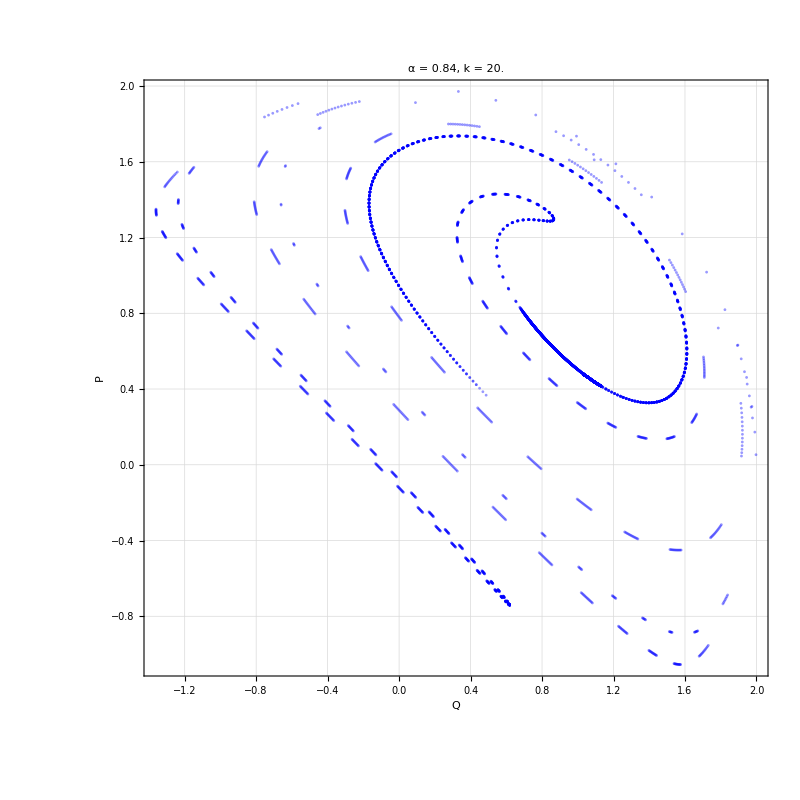

```mathematica
kicks=8;
k=20.;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->All,AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800]
```

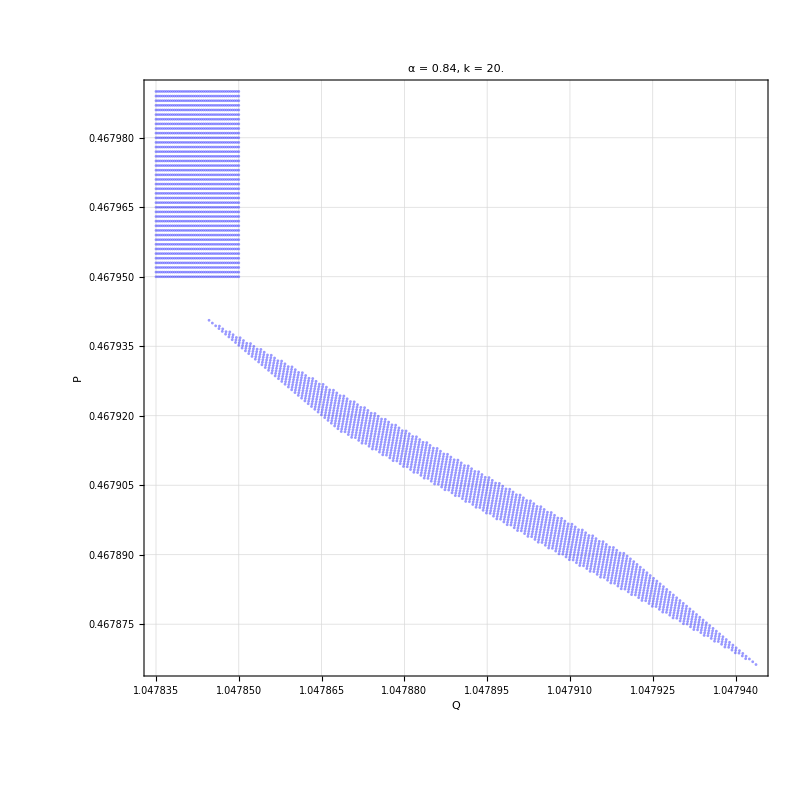

```mathematica
kicks=1;
k=20.;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->All,AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800]
```

```mathematica
kicks=1000;
k=20.;
(*θ=-α/2;*)
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregionb}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarea=Graphics[{PointSize[0.0025],Black,Opacity[0.2],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,45,Black],Style[", n ="<>ToString[kicks],45,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

```mathematica
Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];
Export["poincare_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]];
```

```mathematica
Export["poincare_zoom_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{0.8,1.2},{0.7,0.3}}]];
```

```mathematica
(*Define the map and its Jacobian*)standardMap[{x_,y_},K_]:=Module[{yn,xn},yn=y+K Sin[x];
xn=Mod[x+yn,2 Pi];
{xn,yn}];

jacobianStandardMap[{x_,y_},K_]:=Module[{dx,dy},dx=1+K Cos[x];
dy=1;
{{dx,dy},{1,1}}];

(*Compute the FTLE*)
Clear[computeFTLE];
computeFTLE[map_,jacobian_,grid_,nSteps_,K_]:=Module[{ftleValues,trajectory,jacobianTrajectory,cumulativeJacobian,singularValues,lambda},(*FTLE computation for each grid point*)ftleValues=ParallelTable[Module[{z0={x,y},z,J,Jcum,singularValueMax},(*Initialize cumulative Jacobian*)Jcum=IdentityMatrix[2];
z=z0;
(*Iterate map and Jacobian*)
Do[J=jacobian[z,K];
Jcum=J.Jcum;(*Accumulate Jacobian product*)z=map[z,K];,{n,1,nSteps}];
(*Compute the largest singular value*)singularValueMax=Max[SingularValueList[Jcum]];
(*FTLE calculation*)lambda=Log[singularValueMax]/nSteps;
lambda],{x,grid[[1,1]],grid[[1,2]],grid[[1,3]]},{y,grid[[2,1]],grid[[2,2]],grid[[2,3]]}];
ftleValues];
```

```mathematica
(*Define grid and parameters*)
grid={{0,2 Pi,0.01},{0,2 Pi,0.01}}; (*{x_min,x_max,dx},{y_min,y_max,dy}*)
K=8.0; (*Parameter for standard map*)
nSteps=2; (*Number of iterations*)
(*Compute FTLE*)
ftleMatrix=computeFTLE[standardMap,jacobianStandardMap,grid,nSteps,K];
```

```mathematica
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic,ImageSize->800]
```

```mathematica
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic,ImageSize->800]
```

```mathematica
(*Define grid and parameters*)
grid={{0,2 Pi,0.01},{0,2 Pi,0.01}}; (*{x_min,x_max,dx},{y_min,y_max,dy}*)
K=2.0; (*Parameter for standard map*)
nSteps=10; (*Number of iterations*)
(*Compute FTLE*)
ftleMatrix=computeFTLE[standardMap,jacobianStandardMap,grid,nSteps,K];
(*Visualize FTLE as a heatmap*)
ArrayPlot[ftleMatrix,ColorFunction->"BlueGreenYellow",PlotRange->{Min[ftleMatrix],Max[ftleMatrix]},FrameTicks->{Automatic,Automatic},FrameLabel->{"x","y"},PlotLegends->Automatic]
```

-Graphics-

```mathematica
kicks=20000;
k=20.;
θ=-α/2;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
selectedPoints=Select[newpoincarea,(0.9<=#[[1]]<=1.1)&&(0.4<=#[[2]]<=0.6)&];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[selectedPoints]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregionb}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
selectedPoints=Select[newpoincarea,(0.9<=#[[1]]<=1.1)&&(0.4<=#[[2]]<=0.6)&];
(*newpoincarea=(rot[θ].#&/@newpoincarea);*)
poincarea=Graphics[{PointSize[0.0025],Black,Opacity[0.2],Point[selectedPoints]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,45,Black],Style[", n ="<>ToString[kicks],45,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

```mathematica
Export["poincare_zoom_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->1000,PlotRange->{{0.9,1.1},{0.4,0.6}}]];
```

## Lyapunov

## Definiciones

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];

Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=mapeo[Qini,α,k,n]=Module[{a,list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=mapeob[Qini,α,k,n]=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

Clear[MDpf,MDpb];
MDpf[Qini_,n_,d_]:=Module[{orbit=mapeo[Qini,α,k,n]},
Total[Table[((Abs[orbit[[i+1]][[1]]-orbit[[i]][[1]]])^d+(Abs[orbit[[i+1]][[2]]-orbit[[i+1]][[2]]])^d),{i,1,n}]]
];

MDpb[Qini_,n_,d_]:=Module[{orbit=mapeob[Qini,α,k,n]},
Total[Table[((Abs[orbit[[i+1]][[1]]-orbit[[i]][[1]]])^d+(Abs[orbit[[i+1]][[2]]-orbit[[i+1]][[2]]])^d),{i,1,n}]]
];

Clear[rec];
(*usando norma infinito*)
rec[i_,j_]:=Module[{a=Norm[data[[i]]-data[[j]],Infinity]},
If[a<=ϵ,1,0]
];
(*rec[qi_,α_,k_,n_]:=Module[{data=mapeo2[qi,α,k,n]},
Table[If[Norm[data[[i]]-data[[j]],Infinity]<=ϵ,1,0],{i,1,Length[data]},{j,1,Length[data]}]
];*)
(*rec[qi_,α_,k_,n_]:=Module[{data=mapeo2[qi,α,k,n]},
SparseArray[{{i_,j_}/;Norm[data[[i]]-data[[j]],Infinity]<=ϵ->1},{n+1,n+1}]
];*)
```

```mathematica
Clear[jmas2];
jmas2[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s,lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
s={};
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[2,2]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];

Clear[jmas3];
jmas3[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s,lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
s={};
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[3,3]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];
(*jmas[Jini_,A_Real,n_Integer]:=Module[{j,list=mapeoJ[N[Jini],N[A],n],data,B=N[Pi/2]},
data=Table[N[M[list[[i]],N[A],N[B]]],{i,1,n}];
j=N[Log[Max[N[Abs[N[Eigenvalues[N[Fold[Dot,data]]]]]]]^(N[1/n])]]
];*)
```

## Lyapunov

```mathematica
Clear[mapeo1,jmas];
mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];

(*jmas[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s,lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
s={};
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[1,1]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];*)

jmas[si_,α_Real,k_Real,n_Integer]:=Module[{xt,q,r,s={},lces,tras=0},
xt=mapeo1[si,α,k,tras];
{q,r}=QRDecomposition[M[si,α,k]];
Do[
xt=mapeo1[xt,α,k,1];
{q,r}=QRDecomposition[M[xt,α,k].Transpose[q]];
(*s=Append[s,Table[r[[i,i]],{i,3}]];*)
s=Append[s,r[[1,1]]];
,{n}];
lces=Rest[FoldList[Plus,0,Re[Log[s]]]]/Range[n];
lces=lces[[2;;n]]
];
```

## Method

```mathematica
{q0,p0}=RandomPoint[Disk[{0,0},1.999],1][[1]]
```

{-0.454046,0.705212}

```mathematica
s0=change2[{q0,p0}]
```

{-0.41219,0.640203,-0.648259}

```mathematica
α=0.84;
k=20.;
```

```mathematica
nlist=Range[100];
```

```mathematica
serie=jmas[s0,α,k,1000];
```

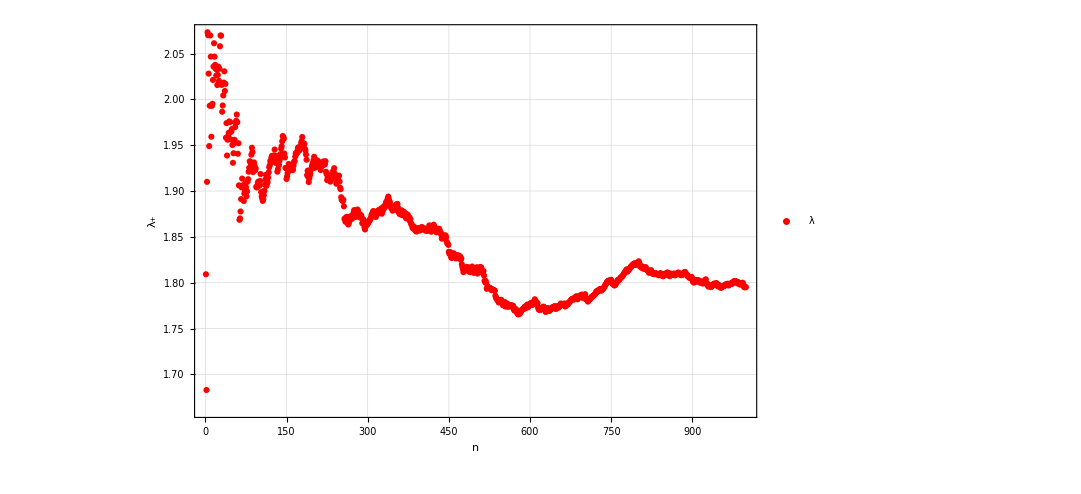

```mathematica
plot1=ListPlot[serie,PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Red,PlotLegends->{Style["λ",20,Black]}]
```

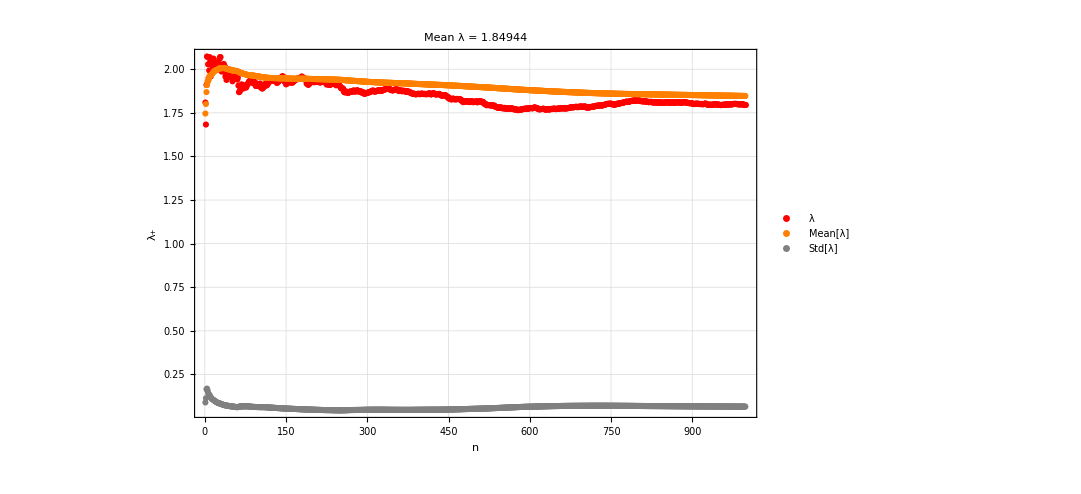

```mathematica
mean={};
std={};
Do[
data1=serie[[1;;i]];
AppendTo[mean,Mean[data1]];
AppendTo[std,StandardDeviation[data1]];
,{i,2,Length[serie]}];
plot2=ListPlot[mean,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Orange,PlotLegends->{Style["Mean[λ]",20,Black]}];
plot3=ListPlot[std,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Gray,PlotLegends->{Style["Std[λ]",20,Black]}];
Show[plot1,plot2,plot3,PlotRange->All,PlotLabel->Style["Mean λ = "<>ToString[Mean[mean[[-100;;-1]]]],30]]
```

## Quantum initial conditions

```mathematica
{x0,x1,y0,y1}={0.9,1.2,0.35,0.6};
region=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/50},{j,y0,y1,(y1-y0)/50}],1];
region//Length
```

2601

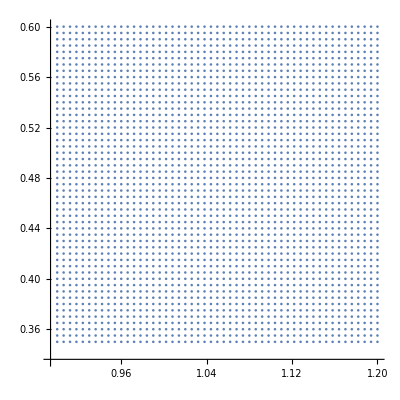

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
{q0,p0}=region[[1000]]
s0=change2[{q0,p0}]
```

{1.014,0.5}

{0.836443,0.412447,-0.360902}

```mathematica
α=0.84;
k=20.;
```

```mathematica
serie=jmas[s0,α,k,10000];
```

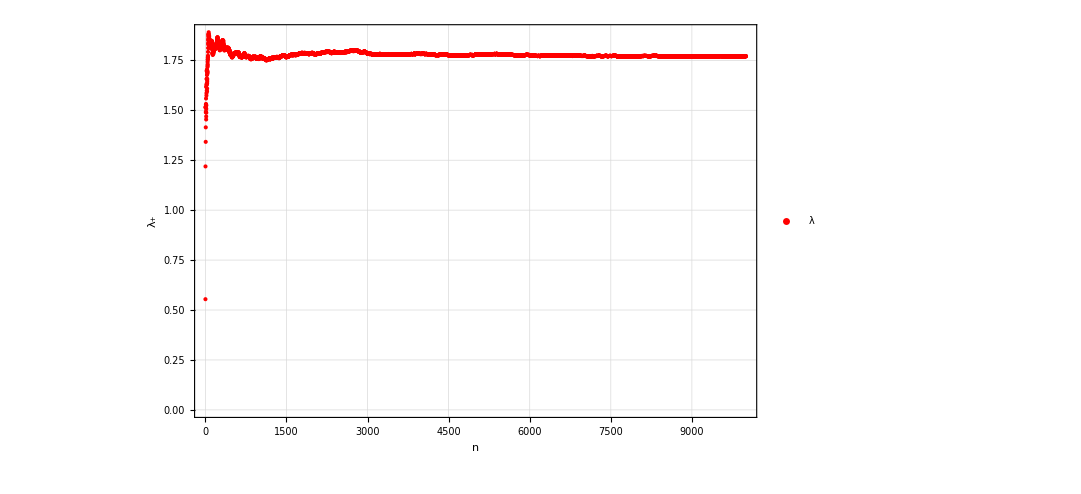

```mathematica
plot1=ListPlot[serie,PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Red,PlotLegends->{Style["λ",20,Black]}]
```

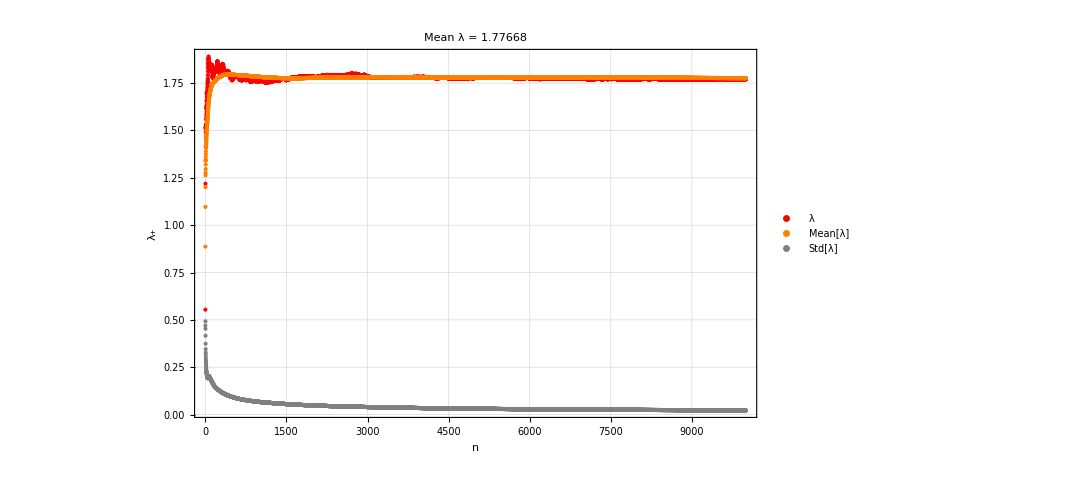

```mathematica
mean={};
std={};
Do[
data1=serie[[1;;i]];
AppendTo[mean,Mean[data1]];
AppendTo[std,StandardDeviation[data1]];
,{i,2,Length[serie]}];
plot2=ListPlot[mean,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Orange,PlotLegends->{Style["Mean[λ]",20,Black]}];
plot3=ListPlot[std,AspectRatio->1/2,PlotTheme->"Scientific",ImageSize->600,PlotStyle->Gray,PlotLegends->{Style["Std[λ]",20,Black]}];
Show[plot1,plot2,plot3,PlotRange->All,PlotLabel->Style["Mean λ = "<>ToString[Mean[mean[[-100;;-1]]]],30]]
```

```mathematica
regions=Table[change2[i],{i,region}];
```

```mathematica
serie=ParallelTable[jmas[i,α,k,1000],{i,regions}];
```

```mathematica
lyapunovs=Table[{region[[i,1]],region[[i,2]],Mean[serie[[i]]]},{i,Length[region]}];
```

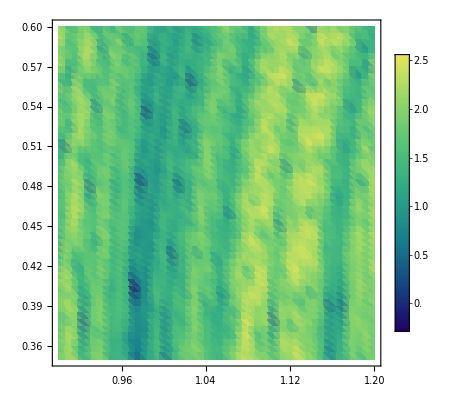

```mathematica
ListDensityPlot[lyapunovs,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow"]
```

```mathematica
Export["lyapunovszoom.png",ListDensityPlot[lyapunovs,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->800]]
```

lyapunovszoom.png

```mathematica
serie//Dimensions
```

{2601,4999}

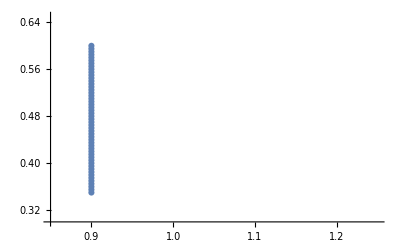

```mathematica
ListPlot[region[[1;;51]],PlotRange->{{x0-0.05,x1+0.05},{y0-0.05,y1+0.05}}]
```

```mathematica
ListPlot[serie[[1;;51]],PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.05]],PlotLegends->{Style["λ",20,Black]}]
```

-Graphics-

```mathematica
plota=ListPlot[serie[[1;;51]],PlotRange->{All,{1.0,2.6}},PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.05]],PlotLegends->{Style["λ",20,Black]}]
```

-Graphics-

```mathematica
region2=Table[{i,j},{i,x0,x1,(x1-x0)/50},{j,y0,y1,(y1-y0)/50}];
```

```mathematica
region2[[1,All]]//Length
region2[[2,All]]//Length
region2[[3,All]]//Length
```

51

51

51

```mathematica
51*51
```

2601

```mathematica
list=Partition[Range[51*51],51];
list//Dimensions
```

{51,51}

```mathematica
index=Range[51];
```

```mathematica
Do[Export["frame"<>ToString[i]<>".png",plota=ListPlot[serie[[list[[i,1]];;list[[i,-1]]]],PlotRange->{All,{1.0,2.6}},PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.05]],PlotLegends->{Style["λ",20,Black]}]],{i,51}]
```

```mathematica
{x0,x1,y0,y1}={1.04783500,1.04785,0.46795,0.467990};
randomregion=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/40},{j,y0,y1,(y1-y0)/40}],1];
randomregion//Length
```

1681

```mathematica
regions2=Table[change2[i],{i,randomregion}];
```

```mathematica
serie2=ParallelTable[jmas[i,α,k,5000],{i,regions2}];
```

```mathematica
lyapunovs2=Table[{region[[i,1]],region[[i,2]],Mean[serie2[[i]][[-500;;-1]]]},{i,Length[regions2]}];
```

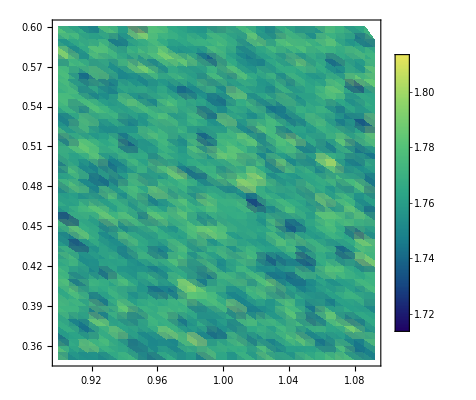

```mathematica
ListDensityPlot[lyapunovs2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow"]
```

```mathematica
Export["lyapunovszoomb.png",ListDensityPlot[lyapunovs2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",ImageSize->800]]
```

lyapunovszoomb.png

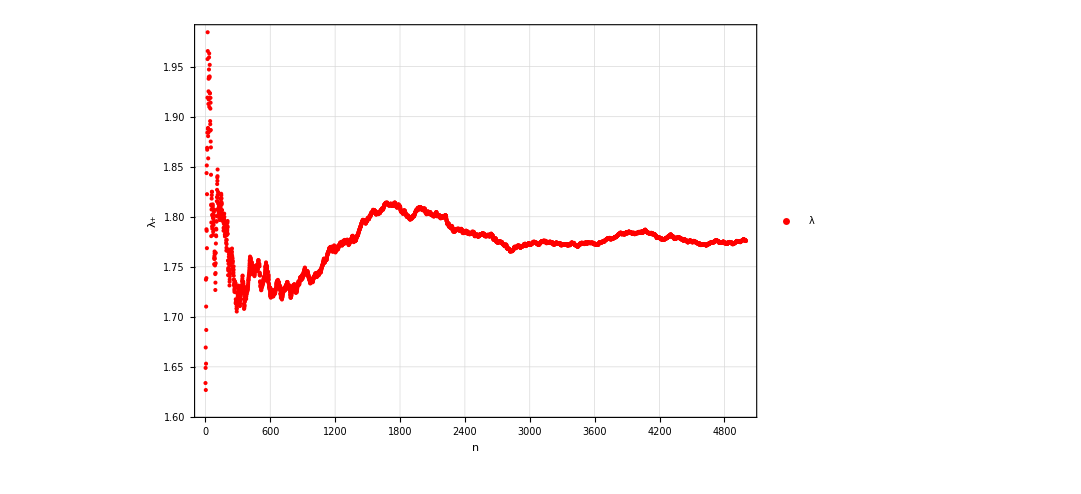

```mathematica
ListPlot[serie2[[1]],PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Red,PlotLegends->{Style["λ",20,Black]}]
```

```mathematica
region2=Table[{i,j},{i,x0,x1,(x1-x0)/40},{j,y0,y1,(y1-y0)/40}];
```

```mathematica
region2[[1,All]]//Length
region2[[2,All]]//Length
region2[[3,All]]//Length
```

41

41

41

```mathematica
41*41
```

1681

```mathematica
list=Partition[Range[41*41],41];
list//Dimensions
```

{41,41}

```mathematica
index=Range[41];
```

```mathematica
Do[Export["frame_zoom"<>ToString[i]<>".png",plota=ListPlot[serie[[list[[i,1]];;list[[i,-1]]]],PlotRange->All,PlotTheme->"Detailed",Frame->True,Axes->False,FrameTicksStyle->20,FrameLabel->{Style["n",40],Style["λ_+",40]}, ImageSize->800,PlotStyle->Directive[Red,Opacity[0.05]],PlotLegends->{Style["λ",20,Black]}]],{i,41}]
```

## Zoom α = 0.84, k = 20.

```mathematica
Clear[Fun];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];
Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];
Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];
Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];

Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
{x0,x1,y0,y1}={1.04783500,1.04785,0.46795,0.467990};
randomregion=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/40},{j,y0,y1,(y1-y0)/40}],1];
randomregion//Length
```

1681

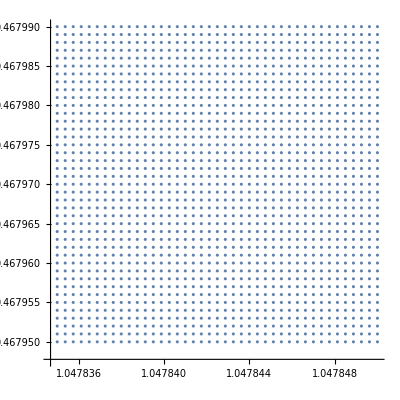

```mathematica
ListPlot[randomregion,AspectRatio->1]
```

```mathematica
kicks=10;
k=20.;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
```

```mathematica
poincarec=ListPlot[newpoincarea,PlotStyle->Directive[Opacity[0.0025],Blue,PointSize[0.0025]],PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",30,Black],Style["P",30,Black]},LabelStyle->Directive[ 25,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},GridLines->Automatic,ImageSize->2000,Frame->True,PlotTheme->"Detailed"];
Export["poincare_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",poincarec];
```

```mathematica
(*Filter points within the region*)
selectedPoints=Select[newpoincarea,(x0<=#[[1]]<=x1)&&(y0<=#[[2]]<=y1)&];
poincarec=ListPlot[selectedPoints,PlotRange->{{x0,x1},{y0,y1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",30,Black],Style["P",30,Black]},LabelStyle->Directive[ 25,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},GridLines->Automatic,ImageSize->2000,Ticks->{Table[{x,StringForm["`1`",NumberForm[x,{8,8}]]},{x,x0,x1,(x1-x0)/10}],Table[{y,StringForm["`1`",NumberForm[y,{6,6}]]},{y,y0,y1,(y1-y0)/10}]}];
Export["poincarezoom_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",poincarec];
```

```mathematica
p=10000;
kicksp=100;
puntosp=ParallelTable[Quiet[mapeop[i,α,k,kicksp,p]],{i,randomregion}];
newpoincarep=ArrayReshape[puntosp,{Length[randomregion]*(kicksp+1),2}];
(*Filter points within the region*)
selectedPointsp=Select[newpoincarep,(x0<=#[[1]]<=x1)&&(y0<=#[[2]]<=y1)&];
poincarep=ListPlot[selectedPointsp,PlotRange->{{x0,x1},{y0,y1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",30,Black],Style["P",30,Black]},LabelStyle->Directive[ 25,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},GridLines->Automatic,ImageSize->2000,Ticks->{Table[{x,StringForm["`1`",NumberForm[x,{8,8}]]},{x,x0,x1,(x1-x0)/10}],Table[{y,StringForm["`1`",NumberForm[y,{6,6}]]},{y,y0,y1,(y1-y0)/10}]}];
Export["poincare_power_p_"<>ToString[p]<>"_period1_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicksp]<>".png",poincarep];
```

# QKT Quantum

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Separating by parity\UPO for alfa 0.84 and k 20

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
QQ[J_]:=Qp[J]+Transpose[Qp[J]];
PP[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Scaling

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],20]]
];
```

```mathematica
{x0,x1,y0,y1}={1.04783500,1.04785,0.46795,0.467990};
region=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/40},{j,y0,y1,(y1-y0)/40}],1];
region//Length
```

1681

```mathematica
Clear[J];
J=1000;
α=0.84;
τ=1;
```

```mathematica
k=20.;
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
```

```mathematica
{q0,p0}={Rationalize[1.04783970],Rationalize[0.467962]};
upo=Quiet[a2iM[J,q0,p0]];
```

```mathematica
upofloq=Conjugate[eigenvecM].upo;
```

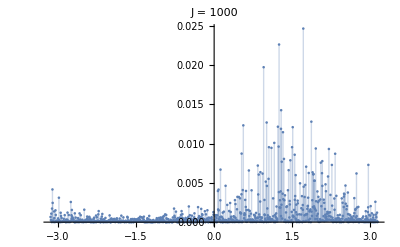

```mathematica
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloq]^2}],PlotRange->All,Filling->Axis,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

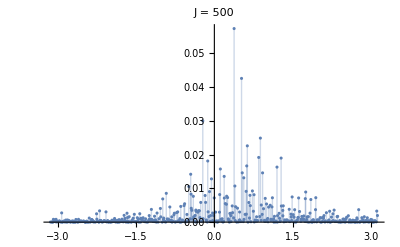

```mathematica
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloq]^2}],PlotRange->All,Filling->Axis,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

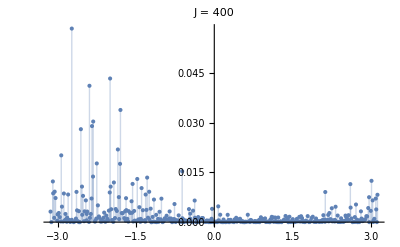

```mathematica
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloq]^2}],PlotRange->All,Filling->Axis,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

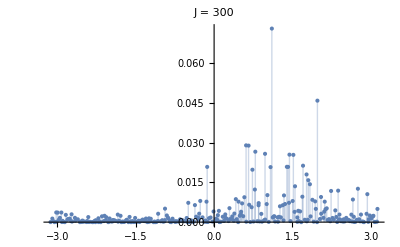

```mathematica
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloq]^2}],PlotRange->All,Filling->Axis,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

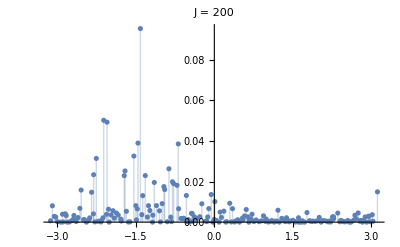

```mathematica
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloq]^2}],PlotRange->All,Filling->Axis,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

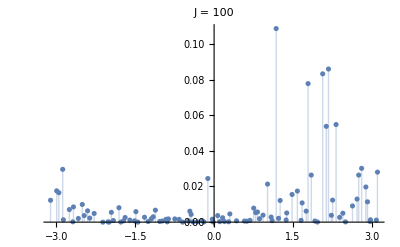

```mathematica
ListPlot[Transpose[{Arg[eigenvalM],Abs[upofloq]^2}],PlotRange->All,Filling->Axis,PlotLabel->Style["J = "<>ToString[J],25,Black]]
```

## Scaling

```mathematica
jlist=Range[1,400];
```

```mathematica
Clear[J];
α=0.84;
τ=1;
k=20.;
{q0,p0}={Rationalize[1.04783970],Rationalize[0.467962]};
```

```mathematica
data={};
Do[

upo=Quiet[a2iM[J,q0,p0]];
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
upofloq=Conjugate[eigenvecM].upo;
AppendTo[data,{J,Total[Abs[upofloq]^4]}];

,{J,jlist}];
Export["ipr_upo_J_"<>ToString[jlist[[-1]]]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>".png",d2plotM]
```

ipr_upo_J_400_alpha_0.84_k_20..png

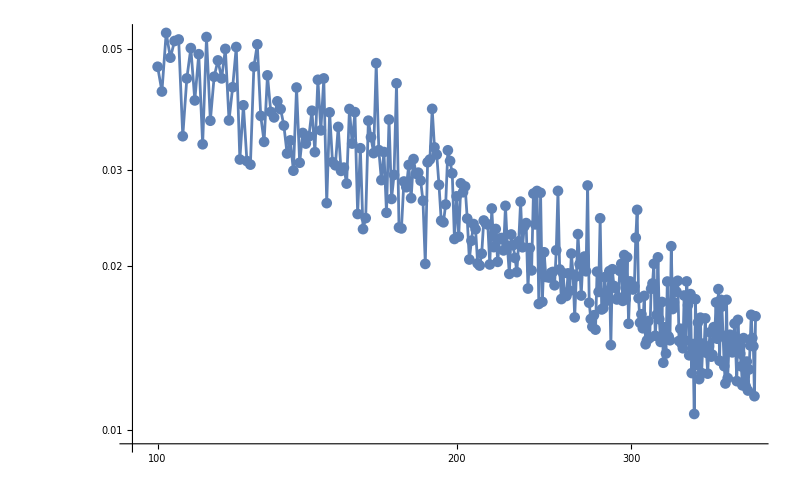

```mathematica
ListLogLogPlot[data[[100;;-1]],PlotRange->All,Joined->True,PlotMarkers->Automatic,ImageSize->800]
```

## Phase space

```mathematica
Clear[J];
α=0.84;
τ=1;
J=50;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2-Pi])Sz[J]];
```

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],20]]
];
Clear[husimiM];
husimiM[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesM[[i]]].ψ]^2},{i,Length[region]}];
(*Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],20]]
];*)
(*cohesm=ParallelTable[Quiet[a2im[J,i[[1]],i[[2]]]],{i,region}];*)
(*husimim[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesm[[i]]].ψ]^2},{i,Length[region]}];*)
```

```mathematica
{x0,x1,y0,y1}={1.04783500,1.04785,0.46795,0.467990};
region=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/80},{j,y0,y1,(y1-y0)/80}],1];
region//Length
```

6561

```mathematica
{x0,x1,y0,y1}={0.9,1.2,0.35,0.6};
region=Flatten[Table[{i,j},{i,x0,x1,(x1-x0)/50},{j,y0,y1,(y1-y0)/50}],1];
region//Length
```

2601

```mathematica
J=1500;
cohesM=ParallelTable[Quiet[a2iM[J,i[[1]],i[[2]]]],{i,region}];
```

```mathematica
k=20.;
(*North pole*)
(*mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;*)
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
(*matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];*)
(*{eigenvalm,eigenvecm}=Eigensystem[matm];*)
(*zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];*)
(*d2m=ParallelTable[Total[Abs[Conjugate[eigenvecm].i]^4],{i,cohesm}];
newd2m=Transpose[{region[[All,1]],region[[All,2]],-Log[d2m]/Log[J]}];
d2plotm=ListDensityPlot[newd2m,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2 -, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
Export["d2minus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[newd2m,PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North D2 -, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]
Export["d2minus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".m",newd2m];*)
(*Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".m",newd2M]*)
```

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvecM].i]^(2q)],{i,cohesM}];
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[J+1]}];
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],35,Black],ImageSize->1500,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,GridLines->Automatic];
Export["d2plus_zoom_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_q_"<>ToString[q]<>"c.png",d2plotM]
```

d2plus_zoom_J_1500_alpha_0.84_k_20._q_2c.png

## D2

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[J];
α=0.84;
τ=1;
k=20.;
```

```mathematica
radius=1.99999;
delta=0.02;
xCoords=Range[0,radius,delta];
yCoords=Range[0,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,Pi/2,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

8000

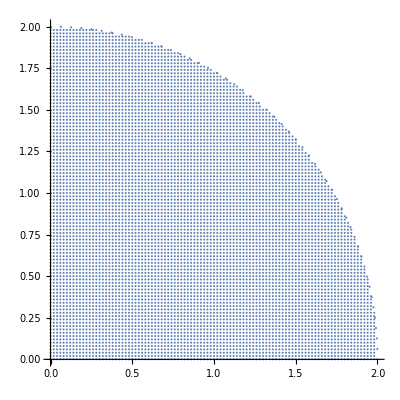

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
newregion=Table[rot[Rationalize[α]/2].i,{i,region}];
```

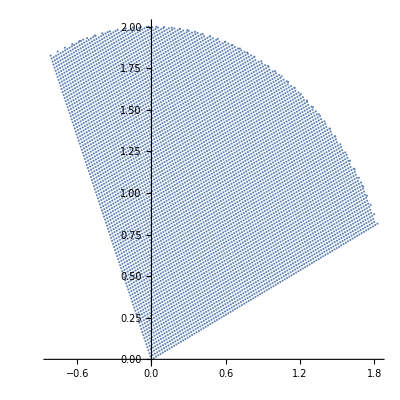

```mathematica
ListPlot[newregion,AspectRatio->1]
```

```mathematica
J=100;
cohesM=ParallelTable[Quiet[a2iM[J,i[[1]],i[[2]]]],{i,newregion}];
```

```mathematica
k=20.;
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
```

```mathematica
q=2;
d2M=ParallelTable[Total[Abs[Conjugate[eigenvecM].i]^(2q)],{i,cohesM}];
```

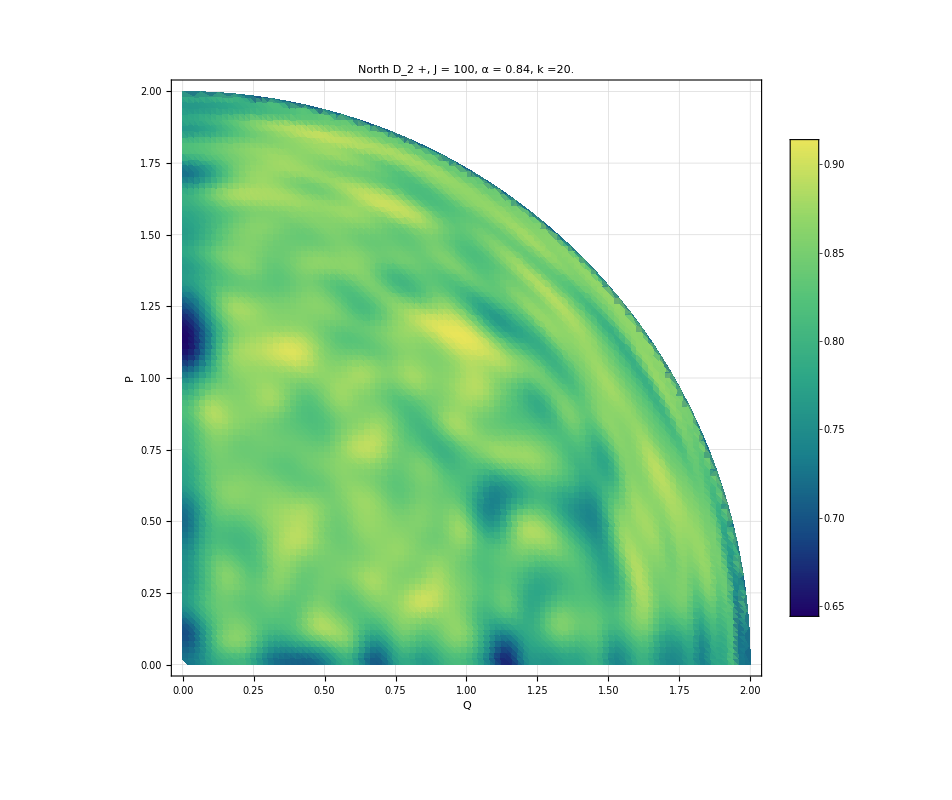

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],(1-q)Log[d2M]/Log[J+1]}];
d2plotM=ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["North D_2 +, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k ="<>ToString[k],35,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,GridLines->Automatic]
```